```mathematica
(* reverse-engineer The Life You Can Save's algorithm *)
```

```mathematica
pairs={{100,1},{1000,10},{5000,50},{6000,60.5},{7000,71},{8000,82},{9000,93},{10000,104},{20000,229},{30000,398},{40000,632},{50000,954},{100000,4628},{154000,8000},{1000000,143450},{10000000,2348450}}
```

{{100,1},{1000,10},{5000,50},{6000,60.5},{7000,71},{8000,82},{9000,93},{10000,104},{20000,229},{30000,398},{40000,632},{50000,954},{100000,4628},{154000,8000},{1000000,143450},{10000000,2348450}}

```mathematica
percs={#[[1]],#[[2]]/#[[1]]}&/@pairs
```

{{100,1/100},{1000,1/100},{5000,1/100},{6000,0.0100833},{7000,71/7000},{8000,41/4000},{9000,31/3000},{10000,13/1250},{20000,229/20000},{30000,199/15000},{40000,79/5000},{50000,477/25000},{100000,1157/25000},{154000,4/77},{1000000,2869/20000},{10000000,46969/200000}}

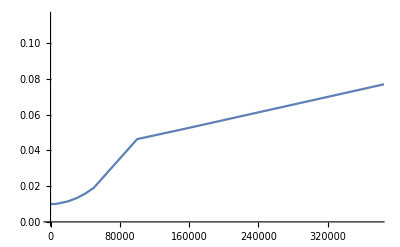

```mathematica
ListLinePlot[percs]
```